# Simple Quantum Tunneling Effect ( Square Barrier )

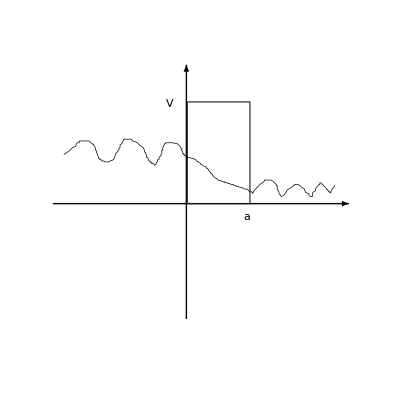

```mathematica
(* we divide the region in 3 *)
(* x < 0 *)
(* 0 < x < a *)
(* a < x *)
(* The Schrodinger Equation is *)
ⅈ ℏ D[ Ψ[x,t],t]== -ℏ^2/(2m) D[Ψ[x,t],{x,2}] + V[x] Ψ[x,t]
```

```mathematica
(* Using space and time seperation *)
Ψ[x,t]== ψ[x]Exp[-ⅈ En/ℏ t]
En ψ[x] == -ℏ^2/(2m) D[ψ[x],{x,2}] + V[x] ψ[x]
```

```mathematica
-(2m)/ℏ^2(En-V[x]) ψ[x] ==  D[ψ[x],{x,2}] 
- k^2 ψ[x] ==  D[ψ[x],{x,2}] 
k^2== (2m)/ℏ^2(En-V[x])
(* For En > V[x], k is real *)
(* For En < V[x], k is imaginary *)
```

```mathematica
(* ON x < 0 *)
(* En > V[x] == 0 *)
(* solution *)
ψA[x_]:= FA Exp[ⅈ k x] + BA Exp[- ⅈ k x];
(* same in x > a *)
ψC[x_]:= FC Exp[ⅈ k x] ;
```

```mathematica
(* on 0 < x < a *)
ψB[x_] := DB Exp[ - kB x ] ;
(* which the increase term cannot be real *)
```

```mathematica
(* by matching the BC *)
ψA[0]== ψB[0]
(D[ψA[x],x]/.x->0)==(D[ψB[x],x]/.x->0)
ψB[a]== ψC[a]
```

BA+FA==DB

-ⅈ BA k+ⅈ FA k==-DB kb

DB ⅇ^(-a kb)==ⅇ^(ⅈ a k) FC

```mathematica
(* By the frist BC *)
Solve[{BA+FA==DB,-ⅈ BA k+ⅈ FA k==-DB kb,DB ⅇ^(-a kb)==ⅇ^(ⅈ a k) FC},{BA,FC,DB}]
```

{{FC→(2 ⅇ^(-ⅈ a k-a kb) FA k)/(k+ⅈ kb),BA→-FA+(2 FA k)/(k+ⅈ kb),DB→(2 FA k)/(k+ⅈ kb)}}

```mathematica
(* The Transmission @ BC 1 *)
T =(2 k)/(k+ⅈ kB) (2 k)/(k-ⅈ kB) //Simplify
R = (-1+(2 k)/(k+ⅈ kB))(-1+(2 k)/(k-ⅈ kB))//Simplify
(* AT BC 2 *)
TT=(2 ⅇ^(-ⅈ a k-a kb)  k)/(k+ⅈ kb)(2 ⅇ^(ⅈ a k-a kb)  k)/(k-ⅈ kb)//Simplify
```

(4 k^2)/(k^2+kB^2)

1

(4 ⅇ^(-2 a kb) k^2)/(k^2+kb^2)

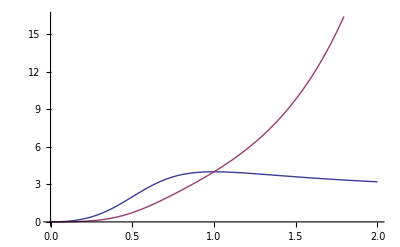

```mathematica
Plot[{(4 k^2)/(k^2+(1-k)^2),(4 ⅇ^(-2 (1-k)) k^2)/(k^2+(1-k)^2)}, {k,0,2}]
```